```mathematica
GG[z_]:=(1+(-9/41 (1+(32 z)/41)+(288 z)/1681) z)/(1-(9/41-z/2) z+(-1+(9 z)/41) z)
GGKenCarp[z_]:=-((2027836641118 (205372066468156589786682646862506005393283957671868081607098129634478034697432259737245152+z (-63172358211281746707151262345751745284607570169718188421714692711306385685801612264524032+z (-48808867189842884167640045981405766425900613210232968394498532488791459801764750086274170+83488993241781845101431048125584968472179772276029318992788503 z))))/(6242886710420635959355167587673092345451645772368478640901182031 (-4055673282236+1767732205903 z)^3))
```

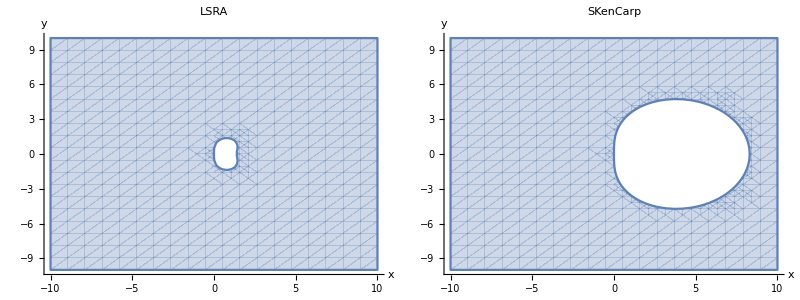

```mathematica
SetOptions[RegionPlot,BaseStyle->{FontFamily->"LM Roman 12",FontSize->22}];
p1 = RegionPlot[{Abs[GG[x+ⅈ y]]<1},{x,-10,10},{y,-10,10},AxesLabel->Automatic,Axes->True,Frame->None,PlotLabel->Style[LSRA,22,FontFamily->"LM Roman 12"],ImageSize->Medium];
p2 = RegionPlot[{Abs[GGKenCarp[x+ⅈ y]]<1},{x,-10,10},{y,-10,10},AxesLabel->Automatic,Axes->True,Frame->None,PlotLabel->Style[SKenCarp,22,FontFamily->"LM Roman 12"],ImageSize->Medium];
Grid[{{p1,p2}}]
```